# qq̄⟶Z^0/γ^*⟶l^+l^-

## Feynman Diagram



```mathematica
R1=CreateTopologies[0, 2 -> 2];
Paint[%];
```

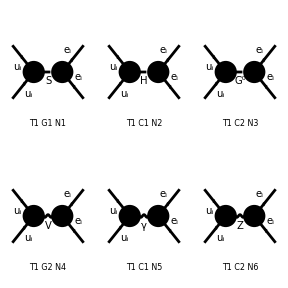

```mathematica
S1=CreateTopologies[0, 2 -> 2];
diags1= InsertFields[R1, {F[3, {i}], -F[3, {i}]} ->
		{F[2, {i}], -F[2, {i}]}];
Paint[%];
```

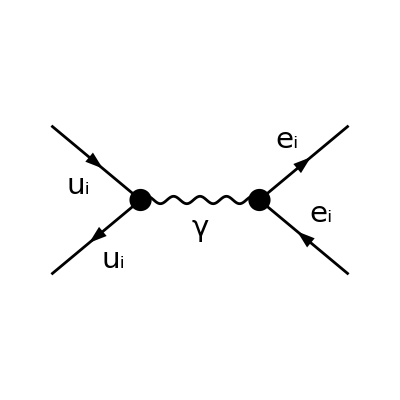

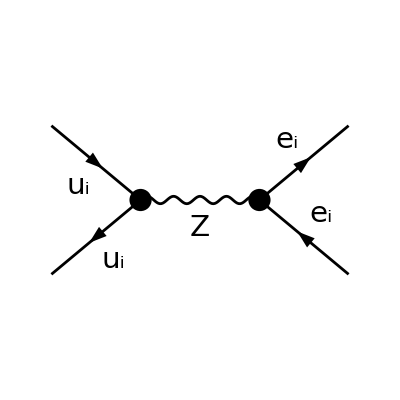

```mathematica
T1=CreateTopologies[0, 2 -> 2];
diagt1 = InsertFields[T1, {F[3, {i}], -F[3, {i}]} ->
		{F[2, {i}], -F[2, {i}]}, InsertionLevel -> {Classes},
		Model -> "SM", ExcludeParticles -> {S[1], S[2]}];
Paint[diagt1, ColumnsXRows -> {1, 1}, Numbering -> None,SheetHeader->None,ImageSize->{256,256}];
```

## Try FeynCalc For Square Amplitude

```mathematica
Amp = FCFAConvert[CreateFeynAmp[diagt1, Truncated -> False],
IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,
ChangeDimension->4,SMP->True, DropSumOver->True,FinalSubstitutions->{Lor1->"μ",Lor2->"ν",MLE[i]->SMP["m_l"],MQU[i]->SMP["m_q"]}]
```

{((ḡ)^μν (φ(OverBar[k1],m_l)).((ⅈ e (γ̄)^ν.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(ⅈ e (γ̄)^ν.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[k2],m_l)) (φ(-OverBar[p2],m_q)).((ⅈ e (γ̄)^μ.(γ̄)^7 δ_Col1Col2 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e (γ̄)^μ.(γ̄)^6 δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))).(φ(OverBar[p1],m_q)))/((OverBar[k1]+OverBar[k2])^2-m_Z^2)}

```mathematica
ComplexConjugate[Amp]
```

{((ḡ)^μν (φ(-OverBar[k2],m_l)).(-(ⅈ e (γ̄)^7.(γ̄)^ν (sin(θ_W)))/(cos(θ_W))-(ⅈ e (γ̄)^6.(γ̄)^ν ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[k1],m_l)) (φ(OverBar[p1],m_q)).((2 ⅈ e (γ̄)^7.(γ̄)^μ δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(ⅈ e (γ̄)^6.(γ̄)^μ δ_Col1Col2 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p2],m_q)))/((OverBar[k1]+OverBar[k2])^2-m_Z^2)}

```mathematica
sqAmpZ =ChangeDimension[(Amp(ComplexConjugate[Amp]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/4]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify, D]
```

{1/(72 (cos(θ_W))^4 (sin(θ_W))^4)e^4 N ((1/((k1+k2)^2-m_Z^2))^2 ((k1·p2) (k2·p1) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)+(k1·p1) (k2·p2) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)-2 (sin(θ_W))^2 (-m_l^2 (2 (sin(θ_W))^2-1) (32 m_q^2 (sin(θ_W))^2 (4 (sin(θ_W))^2-3)+m_Z^2 (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9))+2 m_l^4 (64 (sin(θ_W))^6-80 (sin(θ_W))^4+42 (sin(θ_W))^2-9)+2 m_q^2 (2 m_q^2-m_Z^2) (4 (sin(θ_W))^2-3) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1)))+3 (32 (sin(θ_W))^4-20 (sin(θ_W))^2+3) (1/((k1+k2)^2-m_Z^2))^2 ((k1·p2) (k2·p1)-(k1·p1) (k2·p2)))}

```mathematica
%/.{SMP["m_l"]->0}
```

{1/(72 (cos(θ_W))^4 (sin(θ_W))^4)e^4 N ((1/((k1+k2)^2-m_Z^2))^2 (8 m_q^2 (k1·k2) (4 (sin(θ_W))^2-3) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (sin(θ_W))^2+(k1·p2) (k2·p1) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)+(k1·p1) (k2·p2) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9))+3 (32 (sin(θ_W))^4-20 (sin(θ_W))^2+3) (1/((k1+k2)^2-m_Z^2))^2 ((k1·p2) (k2·p1)-(k1·p1) (k2·p2)))}

```mathematica
%/.{SMP["m_q"]->0}
```

{1/(72 (cos(θ_W))^4 (sin(θ_W))^4)e^4 N (3 (32 (sin(θ_W))^4-20 (sin(θ_W))^2+3) (1/((k1+k2)^2-m_Z^2))^2 ((k1·p2) (k2·p1)-(k1·p1) (k2·p2))+(1/((k1+k2)^2-m_Z^2))^2 ((k1·p2) (k2·p1) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)+(k1·p1) (k2·p2) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)))}

## Feynman Rules

M_Z = -ⅈ g_Z^2/4 ū(k_1)γ^ν(g_V^l-g_A^l γ^5)v(k_2)(g_μν-(q_μ q_ν)/M_Z^2)1/(q^2-M_z^2)v̄(p_2)γ^μ(g_V^q-g_A^q γ^5)u(p_1)

Split:

M_Z = -ⅈ g_Z^2/(4(q^2-M_z^2))[ū(k_1)g_μν γ^ν(C_V^l-C_A^l γ^5)v(k_2)-q_μ/M_Z^2 ū(k_1)[γ^ν q_ν(C_V^l-C_A^l γ^5)]v(k_2)]v̄(p_2)γ^μ(C_V^q-C_A^q γ^5)u(p_1)

M_Z = -ⅈ g_Z^2/(4(q^2-M_z^2))[ū(k_1)g_μν γ^ν(C_V^l-C_A^l γ^5)v(k_2)-q_μ/M_Z^2 ū(k_1)[(k_(1slash)+k_(2slash))(C_V^l-C_A^l γ^5)]v(k_2)]v̄(p_2)γ^μ(C_V^q-C_A^q γ^5)u(p_1)

Split again through slash terms:

-q_μ/M_Z^2 ū(k_1)[(k_(1slash)+k_(2slash))(C_V^l-C_A^l γ^5)]v(k_2)

= -q_μ/M_Z^2(ū(k_1)k_(1slash)(C_V^l-C_A^l γ^5)v(k_2)+ū(k_1)k_(2slash)(C_V^l-C_A^l γ^5)v(k_2))

Pull k_(2slash) through using anticommutator relationship:

= -q_μ/M_Z^2(ū(k_1)k_(1slash)(C_V^l-C_A^l γ^5)v(k_2)+ū(k_1)(γ^μ k_(2μ)C_V^l-γ^μ k_(2μ)C_A^l γ^5)v(k_2))

= -q_μ/M_Z^2(ū(k_1)k_(1slash)(C_V^l-C_A^l γ^5)v(k_2)+ū(k_1)(C_V^l γ^μ-C_A^l γ^μ γ^5)k_(2μ)v(k_2))

= -q_μ/M_Z^2(ū(k_1)k_(1slash)(C_V^l-C_A^l γ^5)v(k_2)+ū(k_1)(C_V^l γ^μ+C_A^l γ^5 γ^μ)k_(2μ)v(k_2))

= -q_μ/M_Z^2(ū(k_1)k_(1slash)(C_V^l-C_A^l γ^5)v(k_2)+ū(k_1)(C_V^l+C_A^l γ^5)k_(2slash)v(k_2))

Dirac Equations Kill this Entire term assuming massless Leptons:

ū(k_1)(k_(1slash)-m_l)= 0,    ū(k_1)k_(1slash)=0  

(k_(2slash)+m_l)v(k_2)= 0,     k_(2slash) v(k_2)=0

On the other hand, massive Leptons:

ū(k_1)(k_(1slash)-m_l)= 0,    ū(k_1)k_(1slash)=ū(k_1)m_l  

(k_(2slash)+m_l)v(k_2)= 0,     k_(2slash) v(k_2)=-v(k_2)m_l

## Amplitude via Z^0

Massless: m_q=m_l=0

M_Z = ⅈ g_Z^2/(4(q^2-m_Z^2))ū(k_1)γ_μ(C_V^l-C_A^l γ^5)v(k_2)v̄(p_2)γ^μ(C_V^q-C_A^q γ^5)u(p_1)

Massive: m_q,m_l

M_Z = ⅈ g_Z^2/(4(q^2-m_Z^2))ū(k_1)[γ_μ(C_V^l-C_A^l γ^5)-q_μ/M_z^2(m_l(C_V^l-C_A^l γ^5)-(C_V^l-C_A^l γ^5)m_l)]v(k_2)v̄(p_2)γ^μ(C_V^q-C_A^q γ^5)u(p_1)

## Square Amplitude

Massless: m_q=m_l=0

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2))Tr[γ_μ(C_V^l-C_A^l γ^5)k_(2slash)γ_ν(C_V^l-C_A^l γ^5)k_(1slash)].Tr[γ^μ(C_V^q-C_A^q γ^5)p_(1slash)γ^ν(C_V^q-C_A^q γ^5)p_(2slash)]

Massive: m_q,m_l

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2))Tr[Γ_μ(k_(2slash)-m_l)(Γ̄)_ν(k_(1slash)+m_l)].Tr[γ^μ(C_V^q-C_A^q γ^5)(p_(1slash)+m_q)γ^ν(C_V^q-C_A^q γ^5)(p_(2slash)-m_q)]

## Trace Calculations (Massless Initial, Massless Final)

```mathematica
Trace1=Tr[GA[μ].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k2].GA[ν].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k1]];
ChangeDimension[%,D]
%//StandardForm;
Trace2=Tr[GA[μ].(Subscript[c, Vq]-Subscript[c, Aq] GA5).GS[p1].GA[ν].(Subscript[c, Vq]-Subscript[c, Aq] GA5).GS[p2]];
ChangeDimension[%,D]
%//StandardForm;
```

4 (-c_Al^2 g^μν (k1·k2)+c_Al^2 k1^ν k2^μ+c_Al^2 k1^μ k2^ν-2 ⅈ c_Al c_Vl ϵ^μνk1k2-c_Vl^2 g^μν (k1·k2)+c_Vl^2 k1^ν k2^μ+c_Vl^2 k1^μ k2^ν)

4 (-c_Aq^2 g^μν (p1·p2)+c_Aq^2 p1^ν p2^μ+c_Aq^2 p1^μ p2^ν+2 ⅈ c_Aq c_Vq ϵ^μνp1p2-c_Vq^2 g^μν (p1·p2)+c_Vq^2 p1^ν p2^μ+c_Vq^2 p1^μ p2^ν)

```mathematica
ChangeDimension[Trace1*Trace2,D]
```

16 (-c_Al^2 g^μν (k1·k2)+c_Al^2 k1^ν k2^μ+c_Al^2 k1^μ k2^ν-2 ⅈ c_Al c_Vl ϵ^μνk1k2-c_Vl^2 g^μν (k1·k2)+c_Vl^2 k1^ν k2^μ+c_Vl^2 k1^μ k2^ν) (-c_Aq^2 g^μν (p1·p2)+c_Aq^2 p1^ν p2^μ+c_Aq^2 p1^μ p2^ν+2 ⅈ c_Aq c_Vq ϵ^μνp1p2-c_Vq^2 g^μν (p1·p2)+c_Vq^2 p1^ν p2^μ+c_Vq^2 p1^μ p2^ν)

```mathematica
%//Expand//Contract
```

64 c_Al c_Aq c_Vl c_Vq (D^2 (k1·p2) (k2·p1)-D^2 (k1·p1) (k2·p2)-5 D (k1·p2) (k2·p1)+5 D (k1·p1) (k2·p2)+6 (k1·p2) (k2·p1)-6 (k1·p1) (k2·p2))+16 D c_Al^2 c_Aq^2 (k1·k2) (p1·p2)+32 c_Al^2 c_Aq^2 (k1·p2) (k2·p1)+32 c_Al^2 c_Aq^2 (k1·p1) (k2·p2)-64 c_Al^2 c_Aq^2 (k1·k2) (p1·p2)+16 D c_Al^2 c_Vq^2 (k1·k2) (p1·p2)+32 c_Al^2 c_Vq^2 (k1·p2) (k2·p1)+32 c_Al^2 c_Vq^2 (k1·p1) (k2·p2)-64 c_Al^2 c_Vq^2 (k1·k2) (p1·p2)+16 D c_Aq^2 c_Vl^2 (k1·k2) (p1·p2)+32 c_Aq^2 c_Vl^2 (k1·p2) (k2·p1)+32 c_Aq^2 c_Vl^2 (k1·p1) (k2·p2)-64 c_Aq^2 c_Vl^2 (k1·k2) (p1·p2)+16 D c_Vl^2 c_Vq^2 (k1·k2) (p1·p2)+32 c_Vl^2 c_Vq^2 (k1·p2) (k2·p1)+32 c_Vl^2 c_Vq^2 (k1·p1) (k2·p2)-64 c_Vl^2 c_Vq^2 (k1·k2) (p1·p2)

```mathematica
%/.{D->4}
```

64 c_Al c_Aq c_Vl c_Vq (2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]))+32 c_Al^2 c_Aq^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+32 c_Al^2 c_Aq^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])+32 c_Al^2 c_Vq^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+32 c_Al^2 c_Vq^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])+32 c_Aq^2 c_Vl^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+32 c_Aq^2 c_Vl^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])+32 c_Vl^2 c_Vq^2 (OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+32 c_Vl^2 c_Vq^2 (OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])

```mathematica
ChangeDimension[%,D]
```

64 c_Al c_Aq c_Vl c_Vq (2 (k1·p2) (k2·p1)-2 (k1·p1) (k2·p2))+32 c_Al^2 c_Aq^2 (k1·p2) (k2·p1)+32 c_Al^2 c_Aq^2 (k1·p1) (k2·p2)+32 c_Al^2 c_Vq^2 (k1·p2) (k2·p1)+32 c_Al^2 c_Vq^2 (k1·p1) (k2·p2)+32 c_Aq^2 c_Vl^2 (k1·p2) (k2·p1)+32 c_Aq^2 c_Vl^2 (k1·p1) (k2·p2)+32 c_Vl^2 c_Vq^2 (k1·p2) (k2·p1)+32 c_Vl^2 c_Vq^2 (k1·p1) (k2·p2)

```mathematica
%//Factor
```

32 (4 c_Al c_Aq c_Vl c_Vq (k1·p2) (k2·p1)-4 c_Al c_Aq c_Vl c_Vq (k1·p1) (k2·p2)+c_Al^2 c_Aq^2 (k1·p2) (k2·p1)+c_Al^2 c_Aq^2 (k1·p1) (k2·p2)+c_Al^2 c_Vq^2 (k1·p2) (k2·p1)+c_Al^2 c_Vq^2 (k1·p1) (k2·p2)+c_Aq^2 c_Vl^2 (k1·p2) (k2·p1)+c_Aq^2 c_Vl^2 (k1·p1) (k2·p2)+c_Vl^2 c_Vq^2 (k1·p2) (k2·p1)+c_Vl^2 c_Vq^2 (k1·p1) (k2·p2))

```mathematica
%//FullSimplify
```

32 ((k1·p1) (k2·p2) (-4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2))+(k1·p2) (k2·p1) (4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2)))

```mathematica
%//StandardForm
```

32 (Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] (-4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2))+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] (4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2)))

```mathematica
32.((Subscript[c, Al]^2+Subscript[c, Vl]^2 ).(Subscript[c, Aq]^2+Subscript[c, Vq]^2)(Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])+4 Subscript[c, Al] Subscript[c, Aq] Subscript[c, Vl] Subscript[c, Vq](Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]]-Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]))
```

32. ((c_Al^2+c_Vl^2).(c_Aq^2+c_Vq^2) ((k1·p2) (k2·p1)+(k1·p1) (k2·p2))+4 c_Al c_Aq c_Vl c_Vq ((k1·p2) (k2·p1)-(k1·p1) (k2·p2)))

## Trace Calculations (Massless Initial, Massless Final), Stay D = 4 till end

```mathematica
Trace1f=Tr[GA[μ].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k2].GA[ν].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k1]]
Trace2f=Tr[GA[μ].(Subscript[c, Vq]-Subscript[c, Aq] GA5).GS[p1].GA[ν].(Subscript[c, Vq]-Subscript[c, Aq] GA5).GS[p2]]
```

4 (-c_Al^2 (ḡ)^μν (OverBar[k1]·OverBar[k2])+c_Al^2 OverBar[k1]^ν OverBar[k2]^μ+c_Al^2 OverBar[k1]^μ OverBar[k2]^ν-2 ⅈ c_Al c_Vl ϵ^(μν OverBar[k1]OverBar[k2])-c_Vl^2 (ḡ)^μν (OverBar[k1]·OverBar[k2])+c_Vl^2 OverBar[k1]^ν OverBar[k2]^μ+c_Vl^2 OverBar[k1]^μ OverBar[k2]^ν)

4 (-c_Aq^2 (ḡ)^μν (OverBar[p1]·OverBar[p2])+c_Aq^2 OverBar[p1]^ν OverBar[p2]^μ+c_Aq^2 OverBar[p1]^μ OverBar[p2]^ν+2 ⅈ c_Aq c_Vq ϵ^(μν OverBar[p1]OverBar[p2])-c_Vq^2 (ḡ)^μν (OverBar[p1]·OverBar[p2])+c_Vq^2 OverBar[p1]^ν OverBar[p2]^μ+c_Vq^2 OverBar[p1]^μ OverBar[p2]^ν)

```mathematica
Trace1f*Trace2f//Expand//Contract//Factor//FullSimplify
```

32 (4 c_Al c_Aq c_Vl c_Vq ((OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])-(OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]))+c_Aq^2 (c_Al^2+c_Vl^2) ((OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+(OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]))+c_Vq^2 (c_Al^2+c_Vl^2) ((OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1])+(OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2])))

```mathematica
ChangeDimension[%,D]
```

32 (4 c_Al c_Aq c_Vl c_Vq ((k1·p2) (k2·p1)-(k1·p1) (k2·p2))+c_Aq^2 (c_Al^2+c_Vl^2) ((k1·p2) (k2·p1)+(k1·p1) (k2·p2))+c_Vq^2 (c_Al^2+c_Vl^2) ((k1·p2) (k2·p1)+(k1·p1) (k2·p2)))

```mathematica
%//StandardForm
```

32 (Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] (-4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2))+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] (4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2)))

```mathematica
32.((Subscript[c, Al]^2+Subscript[c, Vl]^2 ).(Subscript[c, Aq]^2+Subscript[c, Vq]^2)(Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])+4 Subscript[c, Al] Subscript[c, Aq] Subscript[c, Vl] Subscript[c, Vq](Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]]-Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]))
```

32. ((c_Al^2+c_Vl^2).(c_Aq^2+c_Vq^2) ((k1·p2) (k2·p1)+(k1·p1) (k2·p2))+4 c_Al c_Aq c_Vl c_Vq ((k1·p2) (k2·p1)-(k1·p1) (k2·p2)))

## Trace Calculations (Massive quark Initial, Massless Final), Stay D = 4 till end

```mathematica
Trace1=Tr[GA[μ].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k2].GA[ν].(Subscript[c, Vl]-Subscript[c, Al] GA5).GS[k1]]
Trace2massq=Tr[GA[μ].(Subscript[c, Vq]-Subscript[c, Aq] GA5).(GS[p1]+Subscript[m, q]).GA[ν].(Subscript[c, Vq]-Subscript[c, Aq] GA5).(GS[p2]-Subscript[m, q])]
```

4 (-c_Al^2 (ḡ)^μν (OverBar[k1]·OverBar[k2])+c_Al^2 OverBar[k1]^ν OverBar[k2]^μ+c_Al^2 OverBar[k1]^μ OverBar[k2]^ν-2 ⅈ c_Al c_Vl ϵ^(μν OverBar[k1]OverBar[k2])-c_Vl^2 (ḡ)^μν (OverBar[k1]·OverBar[k2])+c_Vl^2 OverBar[k1]^ν OverBar[k2]^μ+c_Vl^2 OverBar[k1]^μ OverBar[k2]^ν)

4 (c_Aq^2 m_q^2 (ḡ)^μν-c_Aq^2 (ḡ)^μν (OverBar[p1]·OverBar[p2])+c_Aq^2 OverBar[p1]^ν OverBar[p2]^μ+c_Aq^2 OverBar[p1]^μ OverBar[p2]^ν+2 ⅈ c_Aq c_Vq ϵ^(μν OverBar[p1]OverBar[p2])-c_Vq^2 m_q^2 (ḡ)^μν-c_Vq^2 (ḡ)^μν (OverBar[p1]·OverBar[p2])+c_Vq^2 OverBar[p1]^ν OverBar[p2]^μ+c_Vq^2 OverBar[p1]^μ OverBar[p2]^ν)

```mathematica
ChangeDimension[Trace1*Trace2massq//Expand//Contract//Factor//FullSimplify,D]
```

32 (m_q^2 (c_Al^2+c_Vl^2) (c_Aq^2-c_Vq^2) (-(k1·k2))+(k1·p1) (k2·p2) (-4 c_Al c_Aq c_Vl c_Vq+c_Aq^2 (c_Al^2+c_Vl^2)+c_Vq^2 (c_Al^2+c_Vl^2))+(k1·p2) (k2·p1) (4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2)))

```mathematica
%//StandardForm
```

32 (Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]] (c_Aq^2 (c_Al^2+c_Vl^2)-4 c_Al c_Aq c_Vl c_Vq+(c_Al^2+c_Vl^2) c_Vq^2)+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]] (4 c_Al c_Aq c_Vl c_Vq+c_Al^2 (c_Aq^2+c_Vq^2)+c_Vl^2 (c_Aq^2+c_Vq^2))-Pair[Momentum[k1,D],Momentum[k2,D]] (c_Al^2+c_Vl^2) (c_Aq^2-c_Vq^2) m_q^2)

```mathematica
32.((Subscript[c, Al]^2+Subscript[c, Vl]^2 ).((Subscript[c, Aq]^2+Subscript[c, Vq]^2)(Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]+Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]])-Pair[Momentum[k1,D],Momentum[k2,D]] (Subscript[c, Aq]^2-Subscript[c, Vq]^2) Subscript[m, q]^2)+4 Subscript[c, Al] Subscript[c, Aq] Subscript[c, Vl] Subscript[c, Vq](Pair[Momentum[k1,D],Momentum[p2,D]] Pair[Momentum[k2,D],Momentum[p1,D]]-Pair[Momentum[k1,D],Momentum[p1,D]] Pair[Momentum[k2,D],Momentum[p2,D]]))
```

32. ((c_Al^2+c_Vl^2).((c_Aq^2+c_Vq^2) ((k1·p2) (k2·p1)+(k1·p1) (k2·p2))-m_q^2 (c_Aq^2-c_Vq^2) (k1·k2))+4 c_Al c_Aq c_Vl c_Vq ((k1·p2) (k2·p1)-(k1·p1) (k2·p2)))

## Square Amplitude after Trace, m_q=m_l=0

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2))32. (((C_V^l)^2+(C_A^l)^2).((C_V^q)^2+(C_A^q)^2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2))+4 c_Al c_Aq c_Vl c_Vq ((k_1·p_2) (k_2·p_1)-(k_1·p_1) (k_2·p_2)))

(|M_Z|)^2=(g_Z^4 E^4)/(64(q^2-m_Z^2))32. (((C_V^l)^2+(C_A^l)^2).((C_V^q)^2+(C_A^q)^2) (2+2cos^2(θ))+16 c_Al c_Aq c_Vl c_Vq cos(θ))

(|M_Z|)^2=(g_Z^4 E^4)/(q^2-m_Z^2) (((C_V^l)^2+(C_A^l)^2).((C_V^q)^2+(C_A^q)^2) ( 1+cos^2(θ) )+8 c_Al c_Aq c_Vl c_Vq cos(θ))

From Kinematics Center of Mass (CM):

p_1=(E,|p_1|)=(E,0,0,p)
p_2=(E,-|p_1|)=(E,0,0,-p)
k_1=(E,|k_1|)=(E,E sin(θ),0,E cos(θ))
k_2=(E,-|k_1|)=(E,E sin(θ),0,E cos(θ))

-2(k_1·p_2) =-2(E^2+Ep cos(θ))=-2(E^2( 1+cos(θ) ))
-2(k_2·p_1) =-2(E^2+Ep cos(θ))=-2(E^2( 1+cos(θ) ))
-2(k_1·p_1) =-2(E^2-Ep cos(θ))=-2(E^2( 1-cos(θ) ))
-2(k_2·p_2) =-2(E^2-Ep cos(θ))=-2(E^2( 1-cos(θ) ))

Keep in mind s-channel:

s = ( p_1+p_2 )^2=( k_1+k_2 )^2 = (p_1)^2+(p_2)^2+2(p_1·p_2) = (p^0)^2-p_1^2+(p_2^0)^2-p_2^2+2 p_1^0 p_2^0-2 p_1 p_2 cos( θ )

   = 2 p_1^0 p_2^0-2 p_1 p_2=2 E^2+2 p_1 p_1=2(E^2+E^2)=2(2 E^2)=(2E)^2=E_cm^2=q^2

## Total Amplitude

(|M|)^2 = (|M_γ|)^2 + (|M_Z|)^2 + M_γ^†M_Z + M_Z^†M_γ

Where:

(|M_γ|)^2 = (1/N_c)e^4(1+cos^2(θ) ) Q_f^2

## Interference with Photon

M_γ = -ⅈ (Q_l Q_q e^2)/q^2 ū(k_1)γ_μ v(k_2)v̄(p_2)γ^μ u(p_1)

M_γ^† = ⅈ (Q_l Q_q e^2)/q^2 v̄(k_2)γ_ν u(k_1)ū(p_1)γ^ν v(p_2)

M_Z = ⅈ g_Z^2/(4(q^2-m_Z^2))ū(k_1)γ_μ(g_V^l-g_A^l γ^5)v(k_2)v̄(p_2)γ^μ(g_V^q-g_A^q γ^5)u(p_1)

M_Z^† = -ⅈ g_Z^2/(4(q^2-m_Z^2))v̄(k_2)γ_ν(g_V^l-g_A^l γ^5)u(k_1)ū(p_1)γ^ν(g_V^q-g_A^q γ^5)v(p_2)

 M_γ^†M_Z = (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2))Tr[γ_ν(g_V^l-g_A^l γ^5)k_(1slash)γ_μ k_(2slash)].Tr[γ^ν p_(2slash)γ^μ(g_V^q-g_A^q γ^5)p_(1slash)]

M_Z^†M_γ= (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2))Tr[γ_ν(g_V^l-g_A^l γ^5)k_(1slash)γ_μ k_(2slash)].Tr[γ^ν p_(2slash)γ^μ(g_V^q-g_A^q γ^5)p_(1slash)]

## Trace Calculations For Interference

```mathematica
Trace1fint=Tr[GA[ν].(Subscript[g, Vl]-Subscript[g, Al] GA5).GS[k1].GA[μ].GS[k2]]
Trace2fint=Tr[GA[ν].GS[p2].GA[μ].(Subscript[g, Vq]-Subscript[g, Aq] GA5).GS[p1]]
```

4 (-ⅈ g_Al ϵ^(μν OverBar[k1]OverBar[k2])+g_Vl OverBar[k1]^ν OverBar[k2]^μ+g_Vl OverBar[k1]^μ OverBar[k2]^ν-g_Vl (ḡ)^μν (OverBar[k1]·OverBar[k2]))

4 (ⅈ g_Aq ϵ^(μν OverBar[p1]OverBar[p2])+g_Vq OverBar[p1]^ν OverBar[p2]^μ+g_Vq OverBar[p1]^μ OverBar[p2]^ν-g_Vq (ḡ)^μν (OverBar[p1]·OverBar[p2]))

```mathematica
Trace1fint*Trace2fint//Expand//Contract//Factor//FullSimplify
```

32 ((OverBar[k1]·OverBar[p1]) (OverBar[k2]·OverBar[p2]) (g_Vl g_Vq-g_Al g_Aq)+(OverBar[k1]·OverBar[p2]) (OverBar[k2]·OverBar[p1]) (g_Al g_Aq+g_Vl g_Vq))

```mathematica
ChangeDimension[%,D]
```

32 ((k1·p1) (k2·p2) (g_Vl g_Vq-g_Al g_Aq)+(k1·p2) (k2·p1) (g_Al g_Aq+g_Vl g_Vq))

Same Kinematics

-2(k_1·p_2) =-2(E^2+Ep cos(θ))=-2(E^2( 1+cos(θ) ))
-2(k_2·p_1) =-2(E^2+Ep cos(θ))=-2(E^2( 1+cos(θ) ))
-2(k_1·p_1) =-2(E^2-Ep cos(θ))=-2(E^2( 1-cos(θ) ))
-2(k_2·p_2) =-2(E^2-Ep cos(θ))=-2(E^2( 1-cos(θ) ))

So Trace Calculation

```mathematica
32 ( (E^4(1+cos^2(θ)  -2cos(θ))) (Subscript[g, V]^l Subscript[g, V]^q-Subscript[g, A]^l Subscript[g, A]^q)+(E^4(1+cos^2(θ) +2cos(θ)))(Subscript[g, A]^l Subscript[g, A]^q+Subscript[g, V]^l Subscript[g, V]^q) )

64 E^4 ( (Subscript[g, V]^l Subscript[g, V]^q)(1+cos^2(θ) )  +2 Subscript[g, A]^l Subscript[g, A]^q cos(θ) )
```

## Total Cross Section via Z^0, Identical Masses

dσ/dΩ =   (|M_Z|)^2/(64 π^2 E_cm^2)=(|M_Z|)^2/(64(π^2(2E))^2)

σ = ((2π)g_Z^4 E^2)/(256 π^2 (q^2-M_Z^2)^2)(((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)∫_0^π ( 1+cos^2(θ) )sin(θ)ⅆθ )+8 g_A^l g_A^q g_V^l g_V^q ∫_0^π cos(θ)sin(θ)ⅆθ

σ = (g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)( 2+2/3)

σ = (g_Z^4 E^2)/(48π (q^2-M_Z^2)^2)((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)

## Total Cross Section via Z^0, Initial Massive Quarks but m_l=0

Would this be Allowed?

(|M|)^2=g_Z^4/(64(q^2-M_Z^2)^2)Tr[γ_μ(C_V^l-C_A^l γ^5)k_(2slash)γ_ν(C_V^l-C_A^l γ^5)k_(1slash)].Tr[γ^μ(C_V^q-C_A^q γ^5)(p_(1slash)+m_q)γ^ν(C_V^q-C_A^q γ^5)(p_(2slash)-m_q)]

(|M|)^2=g_Z^4/(64(q^2-M_Z^2)^2)32. (((C_V^l)^2+(C_A^l)^2)[((C_V^q)^2+(C_A^q)^2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-m_q^2 ((C_V^q)^2-(C_A^q)^2) (k_1·k_2)]
       +4 c_Al c_Aq c_Vl c_Vq ((k_1·p_2) (k_2·p_1)-(k_1·p_1) (k_2·p_2)))

From s-channel calculation:

2(p_1·p_2)=2(2 E^2)

(|M|)^2=g_Z^4/(64(q^2-M_Z^2)^2)32. ( ((C_V^l)^2+(C_A^l)^2)[ ((C_V^q)^2+(C_A^q)^2) E^4( 2+2cos^2(θ) )-2 m_q^2 E^2 ((C_V^q)^2-(C_A^q)^2) ) ]+4 c_Al c_Aq c_Vl c_Vq (4cos (θ)) )

(|M|)^2=(g_Z^4 E^4)/((q^2-M_Z^2)^2). ( ((C_V^l)^2+(C_A^l)^2)[ ((C_V^q)^2+(C_A^q)^2)  ( 1+cos^2(θ) )-m_q^2/(2 E^2) ((C_V^q)^2-(C_A^q)^2)  ]+8 c_Al c_Aq c_Vl c_Vq cos (θ) )

Next:

dσ/dΩ =(|M|)^2/(64 π^2 E_cm^2) (|p_f|)/(| p_i|) =(|M|)^2/(64 π^2 E_cm^2)(√(E^2-m_l^2))/(√(E^2-m_q^2))=(E(|M|)^2)/(64 π^2 E_cm^2 √(E^2-m_q^2))=(|M|)^2/(64 π^2 E_cm^2)(1-m_q^2/E^2)^(-1/2)

dσ/dΩ=(g_Z^4 E^4)/(64 π^2(E_cm^2(q^2-M_Z^2))^2)( ((C_V^l)^2+(C_A^l)^2)[ ((C_V^q)^2+(C_A^q)^2)  ( 1+cos^2(θ) )-m_q^2/(2 E^2) ((C_V^q)^2-(C_A^q)^2)  ]+8 c_Al c_Aq c_Vl c_Vq cos (θ) )(1-m_q^2/E^2)^(-1/2)

σ=((2π)g_Z^4 E^2)/(256 π^2 (q^2-M_Z^2)^2)(1-m_q^2/E^2)^(-1/2)( ((C_V^l)^2+(C_A^l)^2)[ ((C_V^q)^2+(C_A^q)^2) ∫_0^π ( 1+cos^2(θ) )sin(θ)ⅆθ -m_q^2/(2 E^2) ((C_V^q)^2-(C_A^q)^2) ∫_0^π sin(θ)ⅆθ  ]+8 c_Al c_Aq c_Vl c_Vq ∫_0^π cos (θ)sin(θ)ⅆθ  )

σ=(g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)(1-m_q^2/E^2)^(-1/2)( ((C_V^l)^2+(C_A^l)^2)[ (8/3)((C_V^q)^2+(C_A^q)^2) -m_q^2/E^2 ((C_V^q)^2-(C_A^q)^2) ]  )

Expanded for E >> m_q

```mathematica
Series[(1-x)^(-1/2),{x,0,4}]
```

1+x/2+(3 x^2)/8+(5 x^3)/16+(35 x^4)/128+O(x^5)

σ=(g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)(1+1/2 m_q^2/E^2+3/8(m_q^2/E^2)^2+...)( ((C_V^l)^2+(C_A^l)^2)[ (8/3)((C_V^q)^2+(C_A^q)^2) -m_q^2/E^2 ((C_V^q)^2-(C_A^q)^2) ]  )


σ=(g_Z^4 E^2)/(48π (q^2-M_Z^2)^2)((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2+(C_A^q)^2) -(g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)(m_q^2/E^2)((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2-(C_A^q)^2)
     + (g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)(1/2 m_q^2/E^2+3/8(m_q^2/E^2)^2+...)( ((C_V^l)^2+(C_A^l)^2)[ (8/3)((C_V^q)^2+(C_A^q)^2) -m_q^2/E^2 ((C_V^q)^2-(C_A^q)^2) ]  )

σ=(g_Z^4 E^2)/(48π (q^2-M_Z^2)^2)((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2+(C_A^q)^2) -(m_q^2 g_Z^4)/(128π (q^2-M_Z^2)^2)((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2-(C_A^q)^2)
     + (m_q^2 g_Z^4)/(96π (q^2-M_Z^2)^2)((C_V^l)^2+(C_A^l)^2)((C_V^q)^2+(C_A^q)^2)-(g_Z^4 E^2)/(256π (q^2-M_Z^2)^2)(m_q^2/E^2)^2((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2-(C_A^q)^2)
     + (g_Z^4 E^2)/(128π (q^2-M_Z^2)^2)(m_q^2/E^2)^2((C_V^l)^2+(C_A^l)^2)((C_V^q)^2+(C_A^q)^2)-(3 g_Z^4 E^2)/(1024π (q^2-M_Z^2)^2)(m_q^2/E^2)^3((C_V^l)^2+(C_A^l)^2) ((C_V^q)^2-(C_A^q)^2)+...

## Total Hard Scattering Cross Section (fix)

dσ/dΩ =   (|M|)^2/(64 π^2 E_cm^2)=(|M|)^2/(64(π^2(2E))^2)

dσ/dΩ =1/(64(π^2(2E))^2){  (|M_γ|)^2 + (|M_Z|)^2 + M_γ^†M_Z + M_Z^†M_γ  }

       =1/(64(π^2(2E))^2){  (1/3)^2 e^4(1+cos^2(θ) )Q_f^2+(1/3)^2 (g_Z^4 E^4)/((q^2-m_Z^2)^2) Q_f^2(((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2) ( 1+cos^2(θ) )+8 g_A^l g_A^q g_V^l g_V^q cos(θ)) + (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2))64 E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) ) + (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2))64 E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) )   }

dσ/dΩ =1/(64(π^2(2E))^2){  (1/3)^2 e^4(1+cos^2(θ) )Q_f^2+ (1/3)^2(g_Z^4 E^4)/((q^2-m_Z^2)^2) Q_f^2( ((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)  ( 1+cos^2(θ) )+8 g_A^l g_A^q g_V^l g_V^q cos(θ) ) + (1/2)(Q_l Q_q e^2 g_Z^2)/(q^2 (q^2- m_Z^2))E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) )   }

σ  = (2π)/(64(π^2(2E))^2){  (1/3)^2 e^4(1+cos^2(θ) )Q_f^2+(1/3)^2 (g_Z^4 E^4)/((q^2-m_Z^2)^2)Q_f^2(  ((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)  ( 1+cos^2(θ) )+8 g_A^l g_A^q g_V^l g_V^q cos(θ) ) + (Q_l Q_q e^2 g_Z^2)/(2 q^2 (q^2- m_Z^2))E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) )   }∫_0^π sin(θ)ⅆθ

σ  = (2π)/(256(π^2(E))^2){  (1/3)^2 e^4(1+cos^2(θ) )Q_f^2+(1/3)^2 g_Z^4/((q^2-m_Z^2)^2) E^4((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2) Q_f^2 ( 1+cos^2(θ) )∫_0^π sin(θ)ⅆθ) + (Q_l Q_q e^2 g_Z^2)/(2 q^2 (q^2- m_Z^2))E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  ) ∫_0^π sin(θ)ⅆθ  }

σ  = ((2π)e^4)/(256(π^2(E))^2)(8/3){  (1/3)^2 Q_f^2+ (1/3)^2 (E^4((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w) (q^2-m_Z^2)^2)Q_f^2+ (Q_l Q_q)/(2sin^2(θ_w)cos^2(θ_w)[ q^2 (q^2- m_Z^2) ])E^4  (g_V^l g_V^q)}

σ  = e^4/(48π (E)^2){  (1/3)^2 Q_f^2+ (1/3)^2 (E^4((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w) (q^2-m_Z^2)^2)Q_f^2+ (Q_l Q_q)/(2sin^2(θ_w)cos^2(θ_w)[ q^2 (q^2- m_Z^2) ])E^4  (g_V^l g_V^q)}

With Breit-Wigner:

dσ/dΩ=1/(64(π^2(2E))^2){  (1/3)^2 e^4(1+cos^2(θ) )+ (g_Z^4 E^4)/((q^2-m_Z^2)^2) (((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2) ( 1+cos^2(θ) )+8 g_A^l g_A^q g_V^l g_V^q cos(θ)) + (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2+ⅈ Γ_Z m_Z))64 E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) ) + (1/4)(Q_l Q_q e^2 g_Z^2)/(4 q^2 (q^2- m_Z^2- ⅈ Γ_Z m_Z))64 E^4 ( (g_V^l g_V^q)(1+cos^2(θ) )  +2 g_A^l g_A^q cos(θ) )   }

σ̂ = e^4/(48π E^2){  (1/3)Q_f^2+  (1/3)(E^4((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w)[ (q^2-m_Z^2)^2 + Γ_Z^2 m_Z^2 ])Q_f^2+ (Q_l Q_q)/(4sin^2(θ_w)cos^2(θ_w)[ q^2 (q^2- m_Z^2+ ⅈ Γ_Z m_Z) ])E^4  (g_V^l g_V^q) + (Q_l Q_q)/(4sin^2(θ_w)cos^2(θ_w)[ q^2 (q^2- m_Z^2- ⅈ Γ_Z m_Z) ])E^4  (g_V^l g_V^q) }

## Results

Calculation done via Z^0 with Massless: m_q=m_l=0

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2)^2)Tr[γ_μ(g_V^l-g_A^l γ^5)k_(2slash)γ_ν(g_V^l-g_A^l γ^5)k_(1slash)].Tr[γ^μ(g_V^q-g_A^q γ^5)p_(1slash)γ^ν(g_V^q-g_A^q γ^5)p_(2slash)]

dσ_Z/dΩ =   (|M_Z|)^2/(64 π^2 E_cm^2)=(|M_Z|)^2/(64(π^2(2E))^2)

σ_Z = (g_Z^4 E^2)/(48π (q^2-m_Z^2)^2)((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2)

Calculation done via Z^0 with Massive: m_q,m_l=0

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2)^2)Tr[γ_μ(g_V^l-g_A^l γ^5)k_(2slash)γ_ν(g_V^l-g_A^l γ^5)k_(1slash)].Tr[γ^μ(g_V^q-g_A^q γ^5)(p_(1slash)+m_q)γ^ν(g_V^q-g_A^q γ^5)(p_(2slash)-m_q)]

(|M_Z|)^2=g_Z^4/(64(q^2-m_Z^2)^2)32. (((g_V^l)^2+(g_A^l)^2)[((g_V^q)^2+(g_A^q)^2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-m_q^2 ((g_V^q)^2-(g_A^q)^2) (k_1·k_2)]
       +4 g_Al g_Aq g_Vl g_Vq ((k_1·p_2) (k_2·p_1)-(k_1·p_1) (k_2·p_2)))

(|M_Z|)^2=(g_Z^4 E^4)/((q^2-m_Z^2)^2). ( ((g_V^l)^2+(g_A^l)^2)[ ((g_V^q)^2+(g_A^q)^2)  ( 1+cos^2(θ) )-m_q^2/(2 E^2) ((g_V^q)^2-(g_A^q)^2)  ]+8 g_A^l g_A^q g_V^l g_V^q cos(θ) )

dσ_Z/dΩ =(|M_Z|)^2/(64 π^2 E_cm^2) (|p_f|)/(| p_i|) =(|M_Z|)^2/(64 π^2 E_cm^2)(√(E^2-m_l^2))/(√(E^2-m_q^2))=(E(|M_Z|)^2)/(64 π^2 E_cm^2 √(E^2-m_q^2))=(|M_Z|)^2/(64 π^2 E_cm^2)(1-m_q^2/E^2)^(-1/2)

σ_Z=(g_Z^4 E^2)/(128π (q^2-m_Z^2)^2)(1-m_q^2/E^2)^(-1/2)( ((g_V^l)^2+(g_A^l)^2)[ (8/3)((g_V^q)^2+(g_A^q)^2) -m_q^2/E^2 ((g_V^q)^2-(g_A^q)^2) ]  )

σ_Z=(g_Z^4 E^2)/(48π (q^2-m_Z^2)^2)((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) -(m_q^2 g_Z^4)/(128π (q^2-m_Z^2)^2)((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) 
     + (m_q^2 g_Z^4)/(96π (q^2-m_Z^2)^2)((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) -(g_Z^4 E^2)/(256π (q^2-m_Z^2)^2)(m_q^2/E^2)^2((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) 
     + (g_Z^4 E^2)/(128π (q^2-m_Z^2)^2)(m_q^2/E^2)^2((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) -(3 g_Z^4 E^2)/(1024π (q^2-m_Z^2)^2)(m_q^2/E^2)^3((g_V^l)^2+(g_A^l)^2) ((g_V^q)^2+(g_A^q)^2) +...

Total Hard Scattering Cross Section w/o Breit-Wigner

σ̂ = e^4/(48π (E)^2){  (1/3)Q_q^2+ (1/3) (E^4((g_V^l)^2+(g_A^l)^2).((g_V^q)^2+(g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w) (q^2-m_Z^2)^2)Q_q+ (Q_l Q_q)/(2sin^2(θ_w)cos^2(θ_w)q^2[  (q^2- m_Z^2)^2 ])E^4  (g_V^l g_V^q)  }

Total Hard Scattering Cross Section with Breit-Wigner

σ̂ = e^4/(48π E^2){  (1/N_C)Σ Q_q^2+  (1/N_C) (E^4((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w) [ (q^2-m_Z^2)^2 + Γ_Z^2 m_Z^2 ])Σ Q_q^2+ (Σ Q_l Q_q (q^2-m_Z^2))/(2sin^2(θ_w)cos^2(θ_w)q^2[  (q^2-m_Z^2)^2+ Γ_Z^2 m_Z^2 ])E^4  Σ (g_V^l g_V^q)   }

ŝ = 4 E^2 = q^2
e^2 =  4 π α 

σ̂ = (16 π^2 α^2)/(48π (ŝ/4)){  (1/N_C)Σ Q_q^2+  (1/N_C) (((ŝ)^2/16)((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(sin^4(θ_w)cos^4(θ_w) [  (ŝ - m_Z^2)^2 + Γ_Z^2 m_Z^2 ])Σ Q_q+ (Σ Q_l Q_q (ŝ - m_Z^2))/(2sin^2(θ_w)cos^2(θ_w)s[  (ŝ - m_Z^2)^2 + Γ_Z^2 m_Z^2 ])((ŝ)^2/16) Σ (g_V^l g_V^q)   }

σ̂ = (4π α^2)/(3 ŝ){  (1/N_C)Σ Q_q^2+  (1/N_C) ((ŝ)^2 Σ ((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(16sin^4(θ_w)cos^4(θ_w) [  (ŝ - m_Z^2)^2 + Γ_Z^2 m_Z^2 ])Σ Q_q^2+ (Σ Q_l Q_q (ŝ - m_Z^2))/(32sin^2(θ_w)cos^2(θ_w) [  (ŝ - m_Z^2)^2 + Γ_Z^2 m_Z^2 ])ŝ Σ (g_V^l g_V^q)   }

ŝ =M^2

(d σ̂)/dM^2= (4π α^2)/(3 M^2){  (1/N_C)Σ Q_q^2+(1/N_C)M^4 (Σ ((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(16 sin^4 θ_w cos^4 θ_w [  (M^2-m_Z^2)^2+  ℏ^2 Γ_Z^2 m_Z^2 ])Σ Q_q^2
      +M^2 (Σ Q_l Q_q (M^2-m_Z^2))/(32 sin^2 θ_w cos^2 θ_w [  (M^2-m_Z^2)^2+  ℏ^2 Γ_Z^2 m_Z^2 ]) Σ (g_V^l g_V^q)   }δ (ŝ-M^2) 

with:  ℏ Γ_Z (Z→l^+l^-) =  (g_z^2 M_Z)/(48π)Σ ((g_V^l)^2+ (g_A^l)^2)  and  g_z=e/(sin θ_w cos θ_w)

(d σ̂)/dM^2 = (4π α^2)/(3 N_C M^2){ Σ Q_q^2+Σ Q_q^2(Σ ((g_V^l)^2+ (g_A^l)^2).((g_V^q)^2+ (g_A^q)^2))/(16 sin^4 θ_w cos^4 θ_w [  ( 1- ( m_Z/M^)^2 )^2+  ((ℏ Γ_Z m_Z)/M^2)^2 ])+(N_C Σ (g_V^l g_V^q)Σ Q_l Q_q ( 1-(m_Z/M^)^2 )^2)/(32 sin^2 θ_w cos^2 θ_w [  ( 1- ( m_Z/M^)^2 )^2+  ((ℏ Γ_Z m_Z)/M^2)^2 ])  }δ (ŝ-M^2)

## Check constants for M = 100.0 GeV

```mathematica
Sin[28.75*(π/180)]
Cos[28.75*(π/180)]
sqSin=(Sin[28.75*(π/180)])^2
sqCos =(Cos[28.75*(π/180)])^2
fourSin=(Sin[28.75*(π/180)])^4
0.23135019582658814^2
0.7686498041734119^2
fourCos =(Cos[28.75*(π/180)])^4
α = 1.0/137.04
e = 4π α
mZ = 91.188
sumLep = 2.25417378
sumQuark = 5.04609998
```

0.480989

0.876727

0.23135

0.76865

0.0535229

0.0535229

0.590823

0.590823

0.00729714

0.0916986

91.188

2.25417

5.0461

```mathematica
gZ = e/(Sin[28.75*(π/180)]*Cos[28.75*(π/180)])
```

0.217452

```mathematica
constZ =( sumLep*sumQuark)/(16*fourSin*fourCos)
gZ^2
```

22.4816

0.0472854

```mathematica
decayZ=(gZ^2*mZ/(48π))*sumLep*250
```

16.1139

```mathematica
M1 = 100;
BreitWig=decayZ;
ratio1=mZ/M1;
ratio2=(BreitWig*mZ)/(M1*M1);
sqRatio1=ratio1*ratio1;
sqRatio2=ratio2*ratio2;
```

```mathematica
propZ=1.0/(((1.0-sqRatio1)*(1.0-sqRatio1))+((sqRatio2)*(sqRatio2)))
```

6.7693

```mathematica
contributionZ = constZ*propZ
```

152.184

Interference Term

(N_C Σ (g_V^l g_V^q)Σ Q_l Q_q ( 1-(m_Z/M^)^2 )^2)/(32 sin^2 θ_w cos^2 θ_w [  ( 1- ( m_Z/M^)^2 )^2+  ((ℏ Γ_Z m_Z)/M^2)^2 ]) == (3 N_C^2(2*gVquarkUC + 3*gVquarkDSB)(gVlepton + gVleptonnu)Q_l)/(32 sqSin*sqCos)*((1-ratio1^2)^2)/[(1-(ratio1^2)^)^2+(ratio2)^2]

```mathematica
Nc = 3.0
gVquarkUC =0.5-((4.0/3.0)*sqSin)
gVquarkDSB=-0.5+((2.0/3.0)*sqSin)
gVlepton=-0.5+(2.0*sqSin)
gVleptonnu=0.5
```

3.

0.191533

-0.345767

-0.0372996

0.5

```mathematica
constIntfZ = 3 Nc^2*( (2*gVquarkUC)+(3*gVquarkDSB) )*(gVlepton+gVleptonnu)/(32*sqSin*sqCos)
propIntfZ = ( (1.0-sqRatio1)*(1.0-sqRatio1) )/( ((1.0-sqRatio1)*(1.0-sqRatio1))+((sqRatio2)) )
```

-1.43631

0.0759244

```mathematica
(1.0-sqRatio1)*(1.0-sqRatio1)
(sqRatio2)
((1.0-sqRatio1)*(1.0-sqRatio1))+((sqRatio2))
```

0.0283838

0.345459

0.373843

## Scratch

```mathematica
(1-a)*∫_0^π Cos[θ]^2 Sin[θ]ⅆθ+(1+a)*∫_0^π Sin[θ]ⅆθ
```

(2 (1-a))/3+2 (1+a)

```mathematica
(1-a)*∫_0^π Cos[θ]^2 Sin[θ]ⅆθ+(1+a)*∫_0^π Sin[θ]ⅆθ//Simplify
```

(4 (2+a))/3

```mathematica
∫_0^π Cos[θ]^2 Sin[θ]ⅆθ
```

2/3

```mathematica
∫_0^π Cos[θ]Sin[θ]ⅆθ
```

0

```mathematica
2/3(1-a+3+3a)//FullSimplify
```

(4 (2+a))/3

```mathematica
∫_0^π (1+Cos[θ]^2)Sin[θ]ⅆθ//FullSimplify
```

8/3

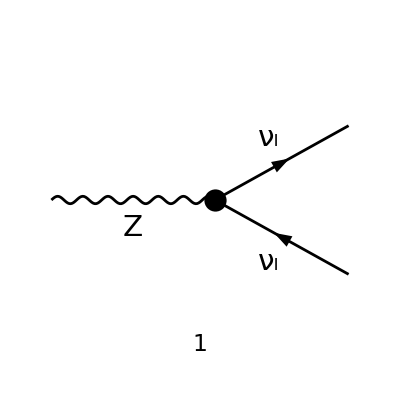

```mathematica
diagsLeptonsMassless=InsertFields[CreateTopologies[0,1->2],{V[2]}->{F[1,{l}],-F[1,{l}]},InsertionLevel->{Classes}];
Paint[diagsLeptonsMassless,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
ampLeptonsMassless=FCFAConvert[CreateFeynAmp[diagsLeptonsMassless],IncomingMomenta->{p},OutgoingMomenta->{l1,l2},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,FinalSubstitutions->{MLE[l]->SMP["m_l"],SMP["e"]->Sqrt[(8/Sqrt[2])*SMP["G_F"]*SMP["m_Z"]^2*SMP["cos_W"]^2*SMP["sin_W"]^2]}]//Contract
```

-(2^(1/4) √(G_F m_Z^2 (cos(θ_W))^2 (sin(θ_W))^2) (φ(OverBar[l1])).(γ̄·ε̄(p)).(γ̄)^7.(φ(-OverBar[l2])))/((cos(θ_W)) (sin(θ_W)))

```mathematica
FCClearScalarProducts[]
SP[p]=SMP["m_Z"]^2;
SP[k1]=SMP["m_q"]^2;
SP[k2]=SMP["m_q"]^2;
SP[p1]=SMP["m_l"]^2;
SP[p2]=SMP["m_l"]^2;
SP[l1]=0;
SP[l2]=0;
SP[k1,k2]=Simplify[(SP[p]-SP[k1]-SP[k2])/2];
SP[p,k1]=Simplify[ExpandScalarProduct[SP[k1+k2,k1]]];
SP[p,k2]=Simplify[ExpandScalarProduct[SP[k1+k2,k2]]];
SP[p1,p2]=Simplify[(SP[p]-SP[p1]-SP[p2])/2];
SP[p,p1]=Simplify[ExpandScalarProduct[SP[p1+p2,p1]]];
SP[p,p2]=Simplify[ExpandScalarProduct[SP[p1+p2,p2]]];
SP[l1,l2]=Simplify[(SP[p]-SP[l1]-SP[l2])/2];
SP[p,l1]=Simplify[ExpandScalarProduct[SP[l1+l2,l1]]];
SP[p,l2]=Simplify[ExpandScalarProduct[SP[l1+l2,l2]]];
SP[p,p]=0;
```

```mathematica
ampSquaredLeptonsMassless[0]=(ampLeptonsMassless(ComplexConjugate[ampLeptonsMassless]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/3]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify
```

1/3 √2 G_F m_Z^2 (2 (OverBar[l1]·ε̄(p)) (OverBar[l2]·(ε̄)^*(p))+2 (OverBar[l1]·(ε̄)^*(p)) (OverBar[l2]·ε̄(p))+2 ⅈ ϵ^(OverBar[l1]OverBar[l2](ε̄)^*(p)ε̄(p))+m_Z^2 (-((ε̄)^*(p)·ε̄(p))))

```mathematica
%//DoPolarizationSums[#,p,0]&
```

2/3 √2 G_F m_Z^4

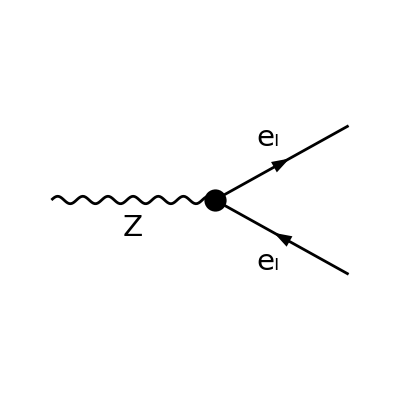

```mathematica
diagsLeptonsMassive=InsertFields[CreateTopologies[0,1->2],{V[2]}->{F[2,{l}],-F[2,{l}]},InsertionLevel->{Classes}];
Paint[diagsLeptonsMassive,ColumnsXRows->{2,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
ampLeptonsMassive=FCFAConvert[CreateFeynAmp[diagsLeptonsMassive],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},List->False,ChangeDimension->4,DropSumOver->True,SMP->True,FinalSubstitutions->{MLE[l]->SMP["m_l"],SMP["e"]->Sqrt[(8/Sqrt[2])*SMP["G_F"]*SMP["m_Z"]^2*SMP["cos_W"]^2*SMP["sin_W"]^2]}]//Contract
```

ⅈ (φ(OverBar[p1],m_l)).((2 ⅈ 2^(1/4) (sin(θ_W)) (γ̄·ε̄(p)).(γ̄)^6 √(G_F m_Z^2 (cos(θ_W))^2 (sin(θ_W))^2))/(cos(θ_W))+(2 ⅈ 2^(1/4) ((sin(θ_W))^2-1/2) (γ̄·ε̄(p)).(γ̄)^7 √(G_F m_Z^2 (cos(θ_W))^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p2],m_l))

```mathematica
ampSquaredLeptonsMassive[0]=(ampLeptonsMassive(ComplexConjugate[ampLeptonsMassive]//FCRenameDummyIndices))//Contract//FermionSpinSum[#, ExtraFactor -> 1/3]&//
		ReplaceAll[#, DiracTrace :> Tr]&//Contract//FullSimplify
```

1/3 √2 G_F m_Z^2 ((2 m_l^2-m_Z^2) ((ε̄)^*(p)·ε̄(p))+4 (2 (sin(θ_W))^2-1) (sin(θ_W))^2 (2 (OverBar[p1]·(ε̄)^*(p)) (OverBar[p2]·ε̄(p))-m_Z^2 ((ε̄)^*(p)·ε̄(p)))+2 (OverBar[p1]·(ε̄)^*(p)) (OverBar[p2]·ε̄(p))+2 (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1) (OverBar[p1]·ε̄(p)) (OverBar[p2]·(ε̄)^*(p))-2 ⅈ (4 (sin(θ_W))^2-1) ϵ^(OverBar[p1]OverBar[p2](ε̄)^*(p)ε̄(p)))

```mathematica
%//DoPolarizationSums[#,p,0]&//Factor//FullSimplify
```

2/3 √2 G_F m_Z^2 (2 m_l^2 (8 (sin(θ_W))^4-4 (sin(θ_W))^2-1)+m_Z^2 (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1))

[  ( 1-(m_Z/M^)^2 )^2+  ((ℏ Γ_Z m_Z)/M^2)^2 ]

```mathematica
Clear[σtot]
```

```mathematica
Convr = 389379.3656
decayZmu= (gZ^2*mZ/(48π))*(  0.5-2(sqSin)+4(fourSin) )
mMu =.106 
s= 7000
```

389379.

0.00718825

0.106

7000

```mathematica
σtot[M_] := (4π α^2)/(3 s)*Convr*(  1+( 0.5-2(sqSin)+4(fourSin) )^2/(fourSin*fourCos)*(1/((1-(mZ/(2M))^2)^2+((decayZmu*mZ)/(2*M)^2)^2))  )
```

```mathematica
σtotlep[M_] := (4π α^2)/(3 s)*Convr*(  1+( sumLep )^2/(fourSin*fourCos)*(1/((1-(mZ/M)^2)^2+((decayZ*mZ)/(M *M))^2))  )
```

```mathematica
Mmax=500.0;
Mmin=2.0;
Npt=500;
M[i_]:=(Mmax-Mmin)/Npt*i+Mmin
```

```mathematica
σtotTable=Table[ { M[i],σtotlep[M[i]] } ,{i,0,Npt} ];
```

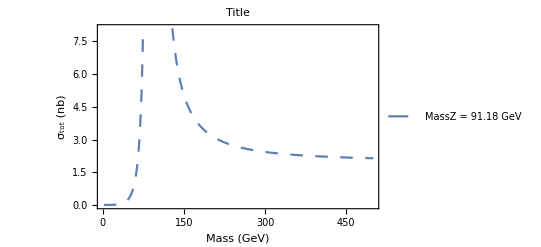

```mathematica
Plotσtot=ListPlot[σtotTable, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"MassZ = 91.18 GeV"},Frame->True,FrameLabel->{"Mass (GeV)","σ_tot (nb)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```